```mathematica
τϵfuncs=NotebookOpen["/Users/rileyhanus/Desktop/Papers/GB_scattering_review/Computation/tau_epsilon-Functions.nb",Visible->True];
SelectionMove[τϵfuncs,All,Notebook];
SelectionEvaluate[τϵfuncs];
```

Material paramters for Si

```mathematica
a=5.4*10^-10; (*(Å) lattice parameter*)
b=a/2^(1/2) ;(*(Å) burgers; vector b = a/2^(1/2)*)
ν=0.27; (*Poisson's ration*)
μ=6.81*10^10;(*(Pa) shear mod; Ref. 1*)
Aniso=1.56; (*Anisotropy factor; Ref. 1*)
κ=3/b;
```

ϵ_Δ(x,y)=du_x/dx+du_y/dy=(-b y (1-2 ν))/(2 π (x^2+y^2) (1-ν))
ϵ_sh=1/2(du_x/dy+du_y/dx)=(b x (x^2-y^2))/(4 π (x^2+y^2)^2 (1-ν))
ϵ_R=(du_x/dy-du_y/dx)=(b x)/(π (x^2+ y^2))

```mathematica
ϵΔxy[x_,y_]:=(-b(1-2ν))/(2π(1-ν))y/(x^2+y^2); 
ϵSHxy[x_,y_]:=b/(4π(1-ν))(x(x^2-y^2))/((x^2+y^2)^2);
ϵRxy[x_,y_]:=b/π x/(x^2+y^2);
ϵxyGB[n_,D_,x_,y_,ϵa_]:=Total[Table[ϵa[x,y+i*D],{i,-n,n,1}]];
```

```mathematica
StrainPlot[ϵfunc_,sizex_,sizey_,int_]:=Module[{},ϵlist=Flatten[Table[{x,y,ϵfunc},{x,-sizex,sizex,int},{y,-sizey,sizey,int}],1];
Print[ListContourPlot[ϵlist,
PlotRange->{All,All,All},
ColorFunction->(*(RGBColor[0.5-0.4*#,0.7-#*0.4,0.5-0.4*(1-#)]&)*)(GrayLevel[0.5-0.3#]&),
ColorFunctionScaling->False,
InterpolationOrder->2,
PlotLegends->Placed[None,Right],
AspectRatio->sizey/sizex,
FrameTicksStyle->{{(*Directive[FontOpacity->0,FontSize->0]*)Automatic,Automatic},{Automatic,Automatic}},
ImageSize->UpTo[250],
Contours->Table[i,{i,-10,10,0.5}],
ContourStyle->GrayLevel[0.5],
FrameStyle->Directive[FontSize->16,Black]]]]
```

```mathematica
BarLegend[{(GrayLevel[0.5-0.3#]&),{-10,10}}]
```

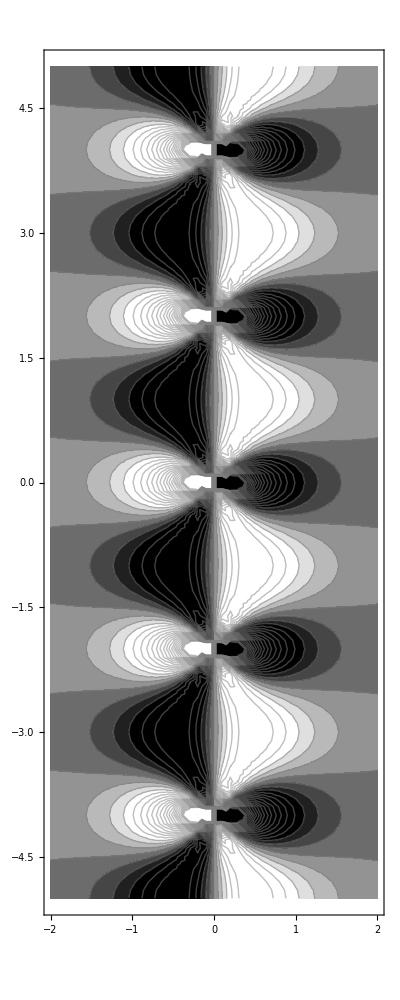

```mathematica
(*StrainPlot[ϵxyGB[4000,2*10^-9,x*10^-9,y*10^-9,ϵΔxy]*10^2,2,5,0.1]*)
StrainPlot[ϵxyGB[200,2*10^-9,x*10^-9,y*10^-9,ϵSHxy]*10^2,2,5,0.1]
(*StrainPlot[ϵSHxy[x*10^-9,y*10^-9]*10^2,15,15,0.1]*)
```

```mathematica
6*5
```

30

0.190919

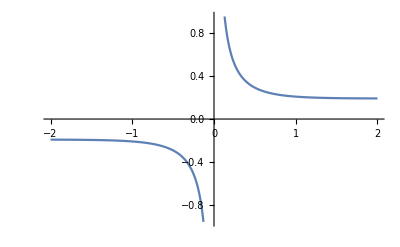

```mathematica
b/(2*10^-9)
Plot[ϵxyGB[200,2*10^-9,x*10^-9,0*10^-9,ϵRxy],{x,-2,2}]
```